## Examples of Bar Charts Data from Capers Jones on the Magnitude of Project Risks

Risks sorted in descending order of magnitude

```mathematica
risks = SortBy[{{"Cancellation", 10.7}, {"Negative ROI", 13.55}, {"Cost Overrun", 12.12}, {"Schedule Slip", 14.26}, {"Unhappy Clients", 16.40}, {"Litigation", 4.99}, {"Financial Risk", 22.33}}, #[[2]] &] // Reverse
```

{{Financial Risk,22.33},{Unhappy Clients,16.4},{Schedule Slip,14.26},{Negative ROI,13.55},{Cost Overrun,12.12},{Cancellation,10.7},{Litigation,4.99}}

```mathematica
riskLabels = risks[[All,1]]
```

{Financial Risk,Unhappy Clients,Schedule Slip,Negative ROI,Cost Overrun,Cancellation,Litigation}

```mathematica
riskMagnitudes = risks[[All,2]]
```

{22.33,16.4,14.26,13.55,12.12,10.7,4.99}

```mathematica
avgAll = Mean[risks[[All,2]]]
```

13.4786

```mathematica
avgNoFin = Mean[Rest[risks[[All,2]]]]
```

12.0033

```mathematica
plotLabel = "Project Risks";
```

### 1. Regular Bar Chart

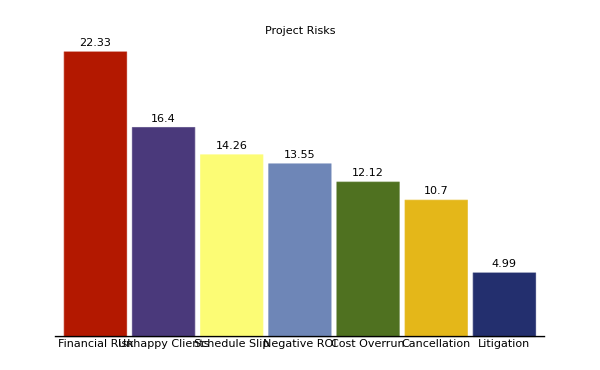

```mathematica
b1 = BarChart[riskMagnitudes,ChartStyle -> 61,Axes-> {True, False}, LabelingFunction->Above, BaseStyle->{FontSize->10,FontFamily->"Helvetica",Bold},ChartLabels -> riskLabels, ImageSize->600, PlotLabel-> plotLabel]
```

The color of the bars can be controlled to a great extent. Here are some examples.

### 2. Bar Charts with Progressively Fading Hues

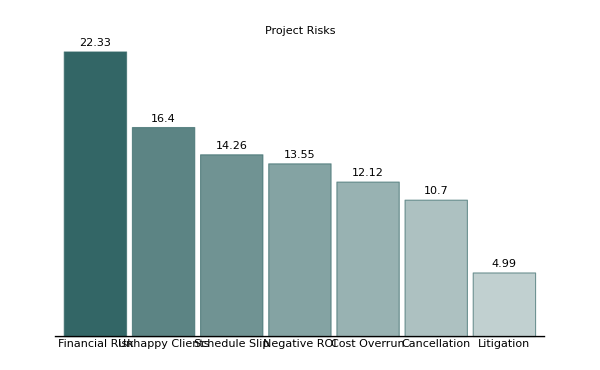
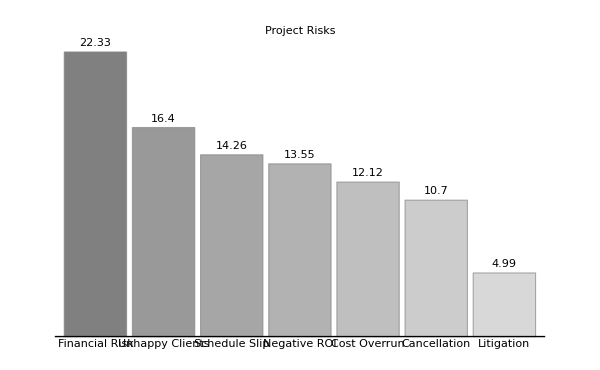
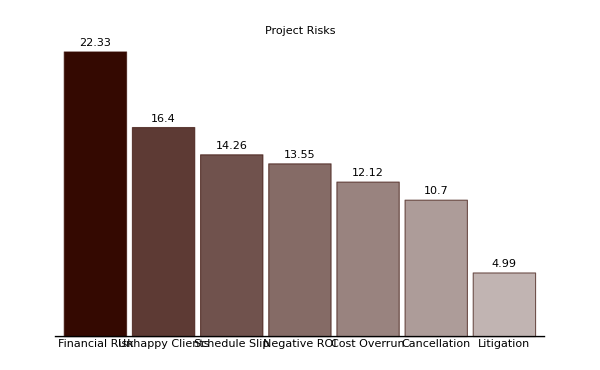

```mathematica
b2 = BarChart[riskMagnitudes,ChartStyle-> {#,{Opacity[1],Opacity[0.8],Opacity[0.7],Opacity[0.6],Opacity[0.5],Opacity[0.4],Opacity[0.3]}},Axes-> {True, False}, LabelingFunction->Above, BaseStyle->{FontSize->10,FontFamily->"Helvetica",Bold},PlotLabel->plotLabel, ChartLabels -> riskLabels, ImageSize->600] & /@ {64, Gray, 25}
```

### 3. Bar Charts with Some Other Color Schemes

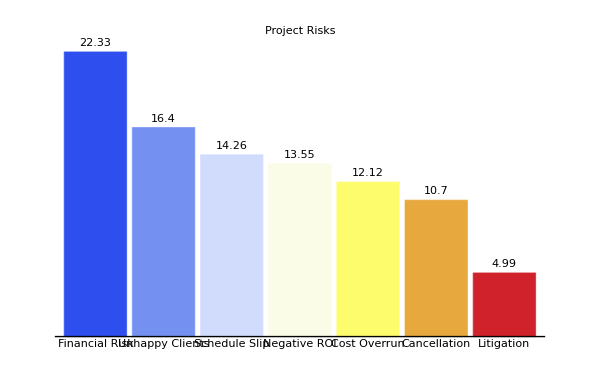
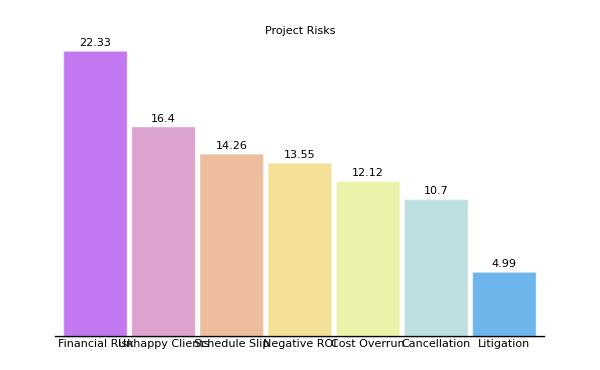
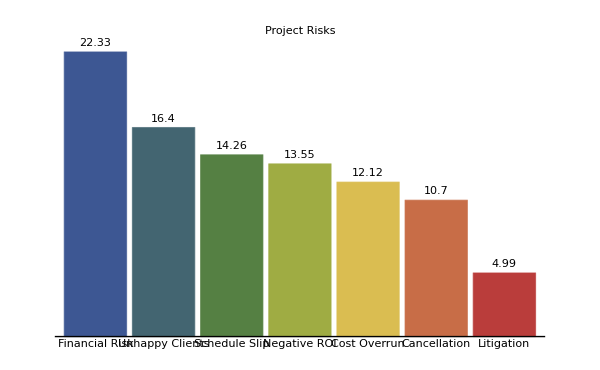

```mathematica
b3 = BarChart[riskMagnitudes,ChartStyle-> #,Axes-> {True, False}, LabelingFunction->Above, BaseStyle->{FontSize->10,FontFamily->"Helvetica",Bold},PlotLabel -> plotLabel, ChartLabels -> riskLabels, ImageSize->600] & /@ {"TemperatureMap","Pastel", "DarkRainbow"}
```

### 4. Bar Chart Oriented to the Right

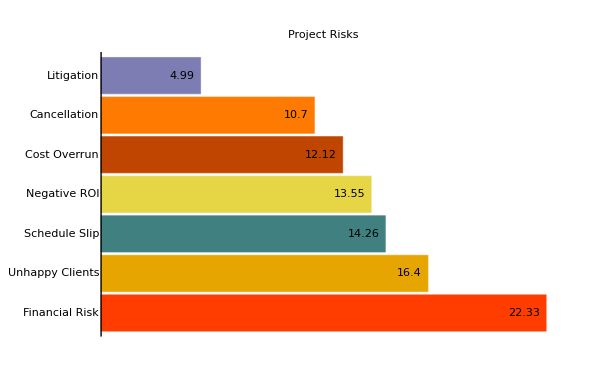

```mathematica
b4 = BarChart[riskMagnitudes,ChartStyle -> 70,Axes-> {True, False}, LabelingFunction->Right, BaseStyle->{FontSize->10,FontFamily->"Helvetica",Bold},PlotLabel -> plotLabel, ChartLabels -> riskLabels, ImageSize->600, BarOrigin->Left]
```

### 5. Bar Chart with Rotated Labels and Mean Line Added

```mathematica
rotatedLabels = Rotate[#,30°, {0.2,0.2}]& /@ riskLabels;
```

```mathematica
b5 = BarChart[riskMagnitudes,ChartStyle -> 55,Axes-> {True, False}, LabelingFunction->Above, BaseStyle->{FontSize->12,FontFamily->"Helvetica",Bold},PlotLabel-> plotLabel, ChartLabels -> rotatedLabels, ImageSize->600];
```

```mathematica
m1 = Plot[avgNoFin, {x, 1, 7}, ImageSize->600, ColorFunction->Function[{x,y},Hue[y]]];
```

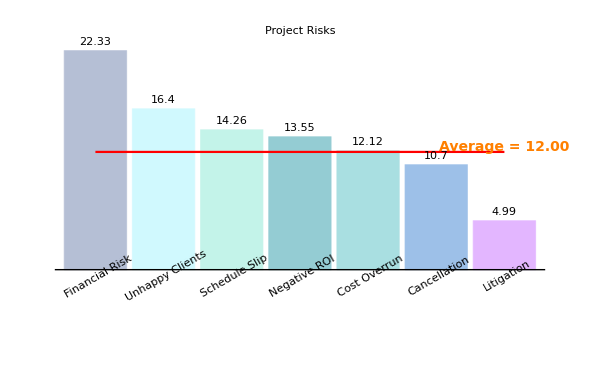

```mathematica
b51 = Show[b5,m1, Epilog->{Text[Style["Average = "<> ToString[NumberForm[avgNoFin,{3,2}]], Bold, Orange, 14],{7,avgNoFin+0.5}]}]
```

## Normal and Peak Staffing

```mathematica
staffingLabels = {"Function", "Normal # of FTEs", "Peak # of FTEs"};
```

```mathematica
staffing = {{"Programmers", 6,9}, {"Testers", 5,8}, {"Designers", 2,3}, {"Business Analysts", 2,3}, {"Technical Writers", 1,1}, {"Quality Assurance", 1,2}, {"1st Line Managers", 2, 3}, {"Database Admin", 1, 1}, {"Project Office Staff", 0,1}, {"Admin Support", 1,1}, {"Configuration Support", 0,0}, {"Project Librarians", 0,0}, {"2nd Line Managers", 0,1}, {"Estimating Specialists", 0,0}, {"Architects", 0,0}, {"Security Specialists", 0,0}, {"Performance Specialists", 0,0}, {"Function Point Counters", 0,0}, {"Human Factor Specialists", 0,0}, {"3rd Line Managers", 0,0}};
```

### 6. Bar Chart of Normal and Peak Staffing with Legend

```mathematica
staffTypes = staffing[[All,1]]
```

{Programmers,Testers,Designers,Business Analysts,Technical Writers,Quality Assurance,1st Line Managers,Database Admin,Project Office Staff,Admin Support,Configuration Support,Project Librarians,2nd Line Managers,Estimating Specialists,Architects,Security Specialists,Performance Specialists,Function Point Counters,Human Factor Specialists,3rd Line Managers}

```mathematica
rotatedStaffLabels = Rotate[#,90°, {0.2,0.2}]& /@ staffTypes;
```

```mathematica
staffValues = Sort[Drop[#,1] & /@ staffing]//Reverse
```

{{6,9},{5,8},{2,3},{2,3},{2,3},{1,2},{1,1},{1,1},{1,1},{0,1},{0,1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

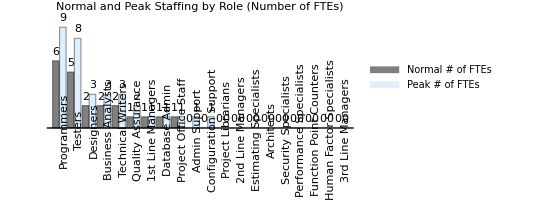

```mathematica
b6 = BarChart[staffValues, ImageSize->400, ChartLabels->{rotatedStaffLabels, None}, ChartLegends->Placed[Drop[staffingLabels, 1], Top], AspectRatio->1/2, ImageSize->600, LabelingFunction->Above, Axes-> {True, False},  BaseStyle->{FontSize->10,FontFamily->"Helvetica",Bold}, ChartStyle-> {Gray, LightBlue}, PlotLabel->"Normal and Peak Staffing by Role \n (Number of FTEs)"]
```

### 7. Line Plot View of Normal and Peak Staffing

```mathematica
tickLabels = Table[{i, rotatedStaffLabels[[i]]}, {i, 1, Length[staffTypes]}];
```

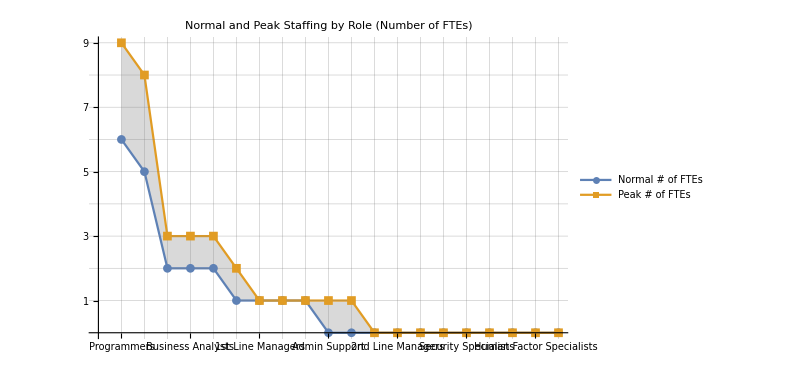

```mathematica
b7 = ListLinePlot[Transpose[staffValues], Ticks-> {tickLabels, Range[10]}, ImageSize->600, PlotRange->All, PlotMarkers-> Automatic, PlotLegends->Placed[Drop[staffingLabels, 1], Top], Filling->{1->{2}},FillingStyle->{LightGray,Blue}, PlotLabel->"Normal and Peak Staffing by Role \n (Number of FTEs)", BaseStyle->{FontSize->10,FontFamily->"Helvetica",Bold}, GridLines-> {Range[Length[staffTypes]], Range[9]}]
```

Similar plots can be made for the number of documentation pages by type of documentation (cells I105 to L117 of the spreadsheet titled “SRM1000RUPAvgGraphics.xlsx”)